```mathematica
w=MapThread[DirectedEdge,Transpose[q]]
```

{1->2,2->1,1->3,2->3,2->4,4->3,4->4}

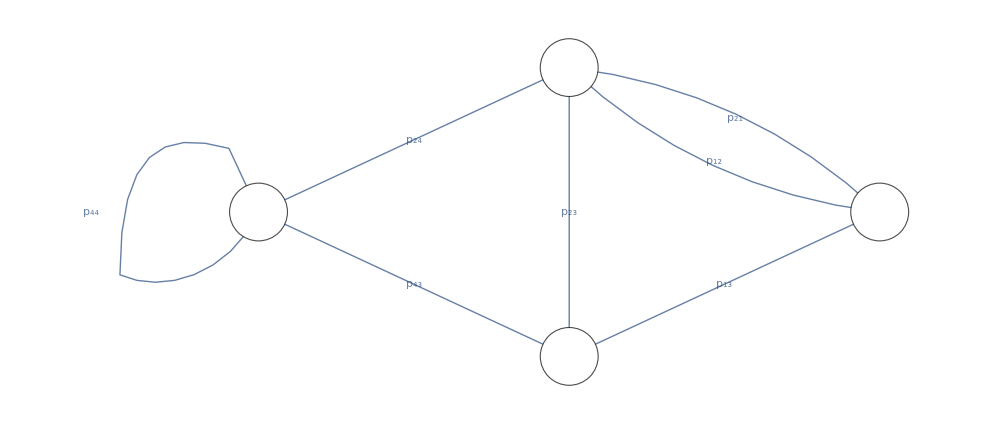

```mathematica
Graph[w,VertexLabels->Placed["Name",Center],VertexSize->0.2,VertexStyle->White,EdgeLabels->MapThread[Rule,Transpose[qq]],ImageSize->1000,EdgeLabelStyle->Directive[FontSize->Scaled[0.03]],VertexLabelStyle->Directive[FontSize->Scaled[0.03]]]
```

```mathematica
q=Partition[{1,2,2,1,1,3,2,3,2,4,4,3,4,4},{2}]
```

{{1,2},{2,1},{1,3},{2,3},{2,4},{4,3},{4,4}}

```mathematica
Table[Subscript[p, i[[1]]*10+i[[2]]],{i,q}]
```

{p_12,p_21,p_13,p_23,p_24,p_43,p_44}

```mathematica
{w,Table[Subscript[p, i[[1]]*10+i[[2]]],{i,w}]}
```

{{1->2,2->1,1->3,2->3,2->4,4->3,4->4},{p_12,p_21,p_13,p_23,p_24,p_43,p_44}}

```mathematica
qq=Transpose[%53]
```

{{1->2,p_12},{2->1,p_21},{1->3,p_13},{2->3,p_23},{2->4,p_24},{4->3,p_43},{4->4,p_44}}

```mathematica
MapThread[Rule,Transpose[qq]]
```

{1->2→p_12,2->1→p_21,1->3→p_13,2->3→p_23,2->4→p_24,4->3→p_43,4->4→p_44}